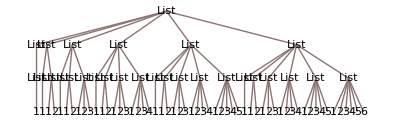

```mathematica
Nest[Range,6,3]//TreeForm
```

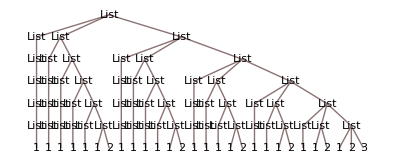

```mathematica
Nest[Range,3,6]//TreeForm
```

```mathematica
Nest[Subsuperscript[#,#,#]&,x,5]
```

((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))_((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))^((((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x))))

长度 4 的 Gray 代码：

```mathematica
Nest[Join[#,Length[#]+Reverse[#]]&,{0},4]
BaseForm[%,2]
```

{0,1,3,2,6,7,5,4,12,13,15,14,10,11,9,8}

{0_2,1_2,11_2,10_2,110_2,111_2,101_2,100_2,1100_2,1101_2,1111_2,1110_2,1010_2,1011_2,1001_2,1000_2}